```mathematica
f1[x_] = x;
```

```mathematica
FunctionPeriod[fn,Reals]
```

0

```mathematica
Plot[,{x,0,20}]
```

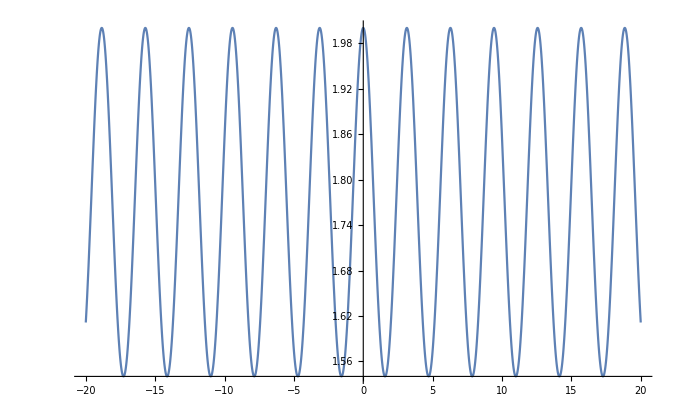

```mathematica
fn=Cos[Sin[x]]+1;

fn1[x_] :=Cos[Sin[x]]+1;
Plot[fn,{x,-20,20}]
```

```mathematica
FunctionPeriod[Sin[Sqrt[2] x]+Sin[x],x]
```

0

```mathematica
max = x/. N[List[Solve[{-20≤x≤20, D[fn,x]==0,D[fn, {x,2}]≤0},x]]]//Flatten;
```

```mathematica
%311
```

{0.,-18.8496,-15.708,-12.5664,-9.42478,-6.28319,-3.14159,3.14159,6.28319,9.42478,12.5664,15.708,18.8496}

```mathematica
%304
```

{0.,-18.8496,-15.708,-12.5664,-9.42478,-6.28319,-3.14159,3.14159,6.28319,9.42478,12.5664,15.708,18.8496}

```mathematica
{0.,3.141592653589793,6.283185307179586,9.42477796076938,12.566370614359172,15.707963267948966,18.84955592153876}
```

{0.,3.14159,6.28319,9.42478,12.5664,15.708,18.8496}

```mathematica
{1.2632578174604474,6.096824059773608,9.441221836175046,14.338864904855477,19.35419340478191}
```

{1.26326,6.09682,9.44122,14.3389,19.3542}

```mathematica
min= x/.  N[List[Solve[{-20≤x≤20, D[fn,x]==0,D[fn, {x,2}]≥ 0},x]]] // Flatten
```

{-17.2788,-14.1372,-10.9956,-7.85398,-4.71239,-1.5708,1.5708,4.71239,7.85398,10.9956,14.1372,17.2788}

```mathematica
max1 = Table[{{max⟦x3⟧,Round[fn/. x-> max⟦x3⟧,0.0001]}},{x3,1,Length[max]}];
max1=  N[Flatten[max1,1]]
```

{{0.,2.},{-18.8496,2.},{-15.708,2.},{-12.5664,2.},{-9.42478,2.},{-6.28319,2.},{-3.14159,2.},{3.14159,2.},{6.28319,2.},{9.42478,2.},{12.5664,2.},{15.708,2.},{18.8496,2.}}

```mathematica
Round[fn /.{ x-> 1},0.01]
```

1.67

```mathematica
Map[f,Range[0,10,.1]]
```

{f[0.],f[0.1],f[0.2],f[0.3],f[0.4],f[0.5],f[0.6],f[0.7],f[0.8],f[0.9],f[1.],f[1.1],f[1.2],f[1.3],f[1.4],f[1.5],f[1.6],f[1.7],f[1.8],f[1.9],f[2.],f[2.1],f[2.2],f[2.3],f[2.4],f[2.5],f[2.6],f[2.7],f[2.8],f[2.9],f[3.],f[3.1],f[3.2],f[3.3],f[3.4],f[3.5],f[3.6],f[3.7],f[3.8],f[3.9],f[4.],f[4.1],f[4.2],f[4.3],f[4.4],f[4.5],f[4.6],f[4.7],f[4.8],f[4.9],f[5.],f[5.1],f[5.2],f[5.3],f[5.4],f[5.5],f[5.6],f[5.7],f[5.8],f[5.9],f[6.],f[6.1],f[6.2],f[6.3],f[6.4],f[6.5],f[6.6],f[6.7],f[6.8],f[6.9],f[7.],f[7.1],f[7.2],f[7.3],f[7.4],f[7.5],f[7.6],f[7.7],f[7.8],f[7.9],f[8.],f[8.1],f[8.2],f[8.3],f[8.4],f[8.5],f[8.6],f[8.7],f[8.8],f[8.9],f[9.],f[9.1],f[9.2],f[9.3],f[9.4],f[9.5],f[9.6],f[9.7],f[9.8],f[9.9],f[10.]}

```mathematica
Map[{(x->#1)}&,Range[0,10,.1]]
```

{{x→0.},{x→0.1},{x→0.2},{x→0.3},{x→0.4},{x→0.5},{x→0.6},{x→0.7},{x→0.8},{x→0.9},{x→1.},{x→1.1},{x→1.2},{x→1.3},{x→1.4},{x→1.5},{x→1.6},{x→1.7},{x→1.8},{x→1.9},{x→2.},{x→2.1},{x→2.2},{x→2.3},{x→2.4},{x→2.5},{x→2.6},{x→2.7},{x→2.8},{x→2.9},{x→3.},{x→3.1},{x→3.2},{x→3.3},{x→3.4},{x→3.5},{x→3.6},{x→3.7},{x→3.8},{x→3.9},{x→4.},{x→4.1},{x→4.2},{x→4.3},{x→4.4},{x→4.5},{x→4.6},{x→4.7},{x→4.8},{x→4.9},{x→5.},{x→5.1},{x→5.2},{x→5.3},{x→5.4},{x→5.5},{x→5.6},{x→5.7},{x→5.8},{x→5.9},{x→6.},{x→6.1},{x→6.2},{x→6.3},{x→6.4},{x→6.5},{x→6.6},{x→6.7},{x→6.8},{x→6.9},{x→7.},{x→7.1},{x→7.2},{x→7.3},{x→7.4},{x→7.5},{x→7.6},{x→7.7},{x→7.8},{x→7.9},{x→8.},{x→8.1},{x→8.2},{x→8.3},{x→8.4},{x→8.5},{x→8.6},{x→8.7},{x→8.8},{x→8.9},{x→9.},{x→9.1},{x→9.2},{x→9.3},{x→9.4},{x→9.5},{x→9.6},{x→9.7},{x→9.8},{x→9.9},{x→10.}}

```mathematica
(x^3+x^2+x+1/.{Map[{(x->#)}&,Range[0,10,.1]]})
```

```mathematica
Transpose@{Range[0,10,.1],(x^3+x^2+x+1/.{Map[{(x->#)}&,Range[0,10,.1]]})//Flatten}
```

```mathematica
fn /. x->
```

```mathematica
ClearAll[min1]
```

```mathematica
min1 =N[Flatten[Table[{{min⟦x3⟧,Round[fn/.x-> min⟦x3⟧,0.0001]}},{x3,1,Length[min]}]],1];
```

```mathematica
%316
```

{-17.2788,1.5403,-14.1372,1.5403,-10.9956,1.5403,-7.85398,1.5403,-4.71239,1.5403,-1.5708,1.5403,1.5708,1.5403,4.71239,1.5403,7.85398,1.5403,10.9956,1.5403,14.1372,1.5403,17.2788,1.5403}

```mathematica
{1.5707963267948966,1.5403,4.71238898038469,1.5403,7.853981633974483,1.5403,10.995574287564276,1.5403,14.137166941154069,1.5403,17.27875959474386,1.5403}
```

{1.5708,1.5403,4.71239,1.5403,7.85398,1.5403,10.9956,1.5403,14.1372,1.5403,17.2788,1.5403}

```mathematica
{3.7646737849311918,-1.4022000000000001,7.696435933454272,-0.006200000000000001,11.82857319404955,-1.5249000000000001,16.864762940718006,-1.8742}
```

{3.76467,-1.4022,7.69644,-0.0062,11.8286,-1.5249,16.8648,-1.8742}

```mathematica
{}
```

{}

```mathematica
{}
```

{}

```mathematica
SortBy[min1,Last]
```

{{16.8648,-1.8742},{11.8286,-1.5249},{3.76467,-1.4022},{7.69644,-0.0062}}

```mathematica
SortBy[max1,Last,Greater]
```

{{14.3389,1.9696},{1.26326,1.9299},{19.3542,1.2689},{9.44122,0.6908},{6.09682,0.5339}}

```mathematica
Length[ Solve[{fn==0 , 0≤ x ≤ 20},x]]
```

9

```mathematica
{min,max}={NMinValue[{D[fn,x],0≤x≤20},x],NMaxValue[{D[fn,x],0≤x≤50},x]};
```

```mathematica
df=Rescale[D[fn,x],{min,max},{0,1}]
```

0.5-1.08445 Cos[x] Sin[Sin[x]]

```mathematica
df/.{{x->1.2632578174604474},{x->3.7}}
```

{0.232387,0.0351797}

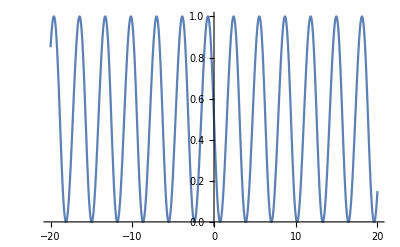

```mathematica
Plot[df,{x,-20,20}]
```

```mathematica
global =x/.N[ List[Solve[{-20≤x≤20, D[fn,x]==0},x]]] // Flatten
```

{0.,-18.8496,-17.2788,-15.708,-14.1372,-12.5664,-10.9956,-9.42478,-7.85398,-6.28319,-4.71239,-3.14159,-1.5708,1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372,15.708,17.2788,18.8496}

```mathematica
global = Sort[global];
```

```mathematica
%357
```

{-18.8496,-17.2788,-15.708,-14.1372,-12.5664,-10.9956,-9.42478,-7.85398,-6.28319,-4.71239,-3.14159,-1.5708,0.,1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372,15.708,17.2788,18.8496}

```mathematica
Length[global]
```

25

```mathematica
global = global[[2;;25]]
```

{-18.8496,-17.2788,-15.708,-14.1372,-12.5664,-10.9956,-9.42478,-7.85398,-6.28319,-4.71239,-3.14159,-1.5708,1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372,15.708,17.2788,18.8496}

```mathematica
global1 = global[[2;;Length[global]]]
```

{-18.8496,-17.2788,-15.708,-14.1372,-12.5664,-10.9956,-9.42478,-7.85398,-6.28319,-4.71239,-3.14159,-1.5708,0.,1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372,15.708,17.2788,18.8496}

```mathematica
global1 = Insert[global1,20,Length[global1]+1]
```

{-18.8496,-17.2788,-15.708,-14.1372,-12.5664,-10.9956,-9.42478,-7.85398,-6.28319,-4.71239,-3.14159,-1.5708,0.,1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372,15.708,17.2788,18.8496,20}

```mathematica
global = Insert[global,-20,1]
```

{-20,-18.8496,-17.2788,-15.708,-14.1372,-12.5664,-10.9956,-9.42478,-7.85398,-6.28319,-4.71239,-3.14159,-1.5708,0.,1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372,15.708,17.2788,18.8496}

```mathematica
intervals = Transpose[{global,global1}]
```

{{-20,-18.8496},{-18.8496,-17.2788},{-17.2788,-15.708},{-15.708,-14.1372},{-14.1372,-12.5664},{-12.5664,-10.9956},{-10.9956,-9.42478},{-9.42478,-7.85398},{-7.85398,-6.28319},{-6.28319,-4.71239},{-4.71239,-3.14159},{-3.14159,-1.5708},{-1.5708,0.},{0.,1.5708},{1.5708,3.14159},{3.14159,4.71239},{4.71239,6.28319},{6.28319,7.85398},{7.85398,9.42478},{9.42478,10.9956},{10.9956,12.5664},{12.5664,14.1372},{14.1372,15.708},{15.708,17.2788},{17.2788,18.8496},{18.8496,20}}

```mathematica
dont = Table[Mean[Table[df/. {x-> x1} , {x1,intervals[[n,1]],intervals[[n,2]],0.01}]],{n,1,Length[intervals]}]
```

{0.864773,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.18449,0.815511,0.135362}

```mathematica
AssociationThread[intervals,dont]
```

<|{0,0.}→0.5,{0.,1.5708}→0.18449,{1.5708,3.14159}→0.815511,{3.14159,4.71239}→0.18449,{4.71239,6.28319}→0.815511,{6.28319,7.85398}→0.18449,{7.85398,9.42478}→0.815511,{9.42478,10.9956}→0.18449,{10.9956,12.5664}→0.815511,{12.5664,14.1372}→0.18449,{14.1372,15.708}→0.815511,{15.708,17.2788}→0.18449,{17.2788,18.8496}→0.815511,{18.8496,50}→0.498849|>

```mathematica
df /. {x-> 1.5708}
```

0.500003

```mathematica
PolynomialQ[fn,x]
```

False

```mathematica
ClearAll[intervals2]
```

```mathematica
ClearAll
```

```mathematica
intervals1 = Table[{x,x+0.1},{x,0,1,0.1}]
```

{{0.,0.1},{0.1,0.2},{0.2,0.3},{0.3,0.4},{0.4,0.5},{0.5,0.6},{0.6,0.7},{0.7,0.8},{0.8,0.9},{0.9,1.},{1.,1.1}}

```mathematica
strings = List["a very sharp decrease","a sharp decrease","a smooth decline","still a smooth decline","still a smooth decline","a very smooth increase","a very smooth increase","a smooth increase","a sharp increase","a very sharp increase"]
```

{a very sharp decrease,a sharp decrease,a smooth decline,still a smooth decline,still a smooth decline,a very smooth increase,a very smooth increase,a smooth increase,a sharp increase,a very sharp increase}

```mathematica
intervals1 = Drop[intervals1,-1]
```

{{0.,0.1},{0.1,0.2},{0.2,0.3},{0.3,0.4},{0.4,0.5},{0.5,0.6},{0.6,0.7},{0.7,0.8},{0.8,0.9},{0.9,1.}}

```mathematica
Exponent[x,x]
```

1

```mathematica
final = Table[{strings[[If[(dont[[x]]≥  0.5),(Round[dont[[x]],0.1]*10)+1, (Round[dont[[x]],0.1]*10 )]]]," that ends at x = ",ToString[intervals[[x,2]]]," then "},{x,1,Length[dont]}]
```

{{a very sharp increase, that ends at x = ,-18.8496, then },{a sharp decrease, that ends at x = ,-17.2788, then },{a sharp increase, that ends at x = ,-15.708, then },{a sharp decrease, that ends at x = ,-14.1372, then },{a sharp increase, that ends at x = ,-12.5664, then },{a sharp decrease, that ends at x = ,-10.9956, then },{a sharp increase, that ends at x = ,-9.42478, then },{a sharp decrease, that ends at x = ,-7.85398, then },{a sharp increase, that ends at x = ,-6.28319, then },{a sharp decrease, that ends at x = ,-4.71239, then },{a sharp increase, that ends at x = ,-3.14159, then },{a sharp decrease, that ends at x = ,-1.5708, then },{still a smooth decline, that ends at x = ,1.5708, then },{a sharp increase, that ends at x = ,3.14159, then },{a sharp decrease, that ends at x = ,4.71239, then },{a sharp increase, that ends at x = ,6.28319, then },{a sharp decrease, that ends at x = ,7.85398, then },{a sharp increase, that ends at x = ,9.42478, then },{a sharp decrease, that ends at x = ,10.9956, then },{a sharp increase, that ends at x = ,12.5664, then },{a sharp decrease, that ends at x = ,14.1372, then },{a sharp increase, that ends at x = ,15.708, then },{a sharp decrease, that ends at x = ,17.2788, then },{a sharp increase, that ends at x = ,18.8496, then },{a very sharp decrease, that ends at x = ,20, then }}

```mathematica
output = "This plot describes the function "
```

```mathematica
Speak[StringJoin[final]]
```

```mathematica
Speak[final]
```

```mathematica
Length[strings]
```

10

```mathematica
Length[intervals1]
```

10

```mathematica
AssociationThread[intervals1,strings]
```

<|{0.,0.1}→a very sharp increase,{0.1,0.2}→a sharp increase,{0.2,0.3}→a smooth increase,{0.3,0.4}→no change,{0.4,0.5}→no change at all,{0.5,0.6}→a very smooth increase,{0.6,0.7}→a very smooth decline,{0.7,0.8}→a smooth decline,{0.8,0.9}→a sharp decline,{0.9,1.}→a very sharp decline|>

```mathematica
dont
```

{0.816341,0.22358,0.670729,0.429007,0.581687,0.306685,0.786787,0.183787,0.760972,0.495442}

AssociationThread::idim: {{0., 0.2, 0}, {0.2, 0.4, 0}, {0.4, 0.6, 0}, {0.6, 0.8, 0}, {0.8, 1., 0}} and {\"\<a very sharp increase\>\", \"\<a sharp increase\>\", \"\<a smooth increase\>\", \"\<no change\>\", \"\<no change at all\>\", \"\<a very smooth increase\>\", \"\<a very smooth decline\>\", \"\<a smooth decline\>\", \"\<a sharp decline\>\", \"\<a very sharp decline\>\"} must have the same length.

AssociationThread[{{0.,0.2,0},{0.2,0.4,0},{0.4,0.6,0},{0.6,0.8,0},{0.8,1.,0}},{a very sharp increase,a sharp increase,a smooth increase,no change,no change at all,a very smooth increase,a very smooth decline,a smooth decline,a sharp decline,a very sharp decline}]

```mathematica
ClearAll[f]
```

```mathematica
f[xa_,na_,sa_]:=
Module[
{df,dont,e,expr,final,fn,fn1,global,global1,HashTable,intervals,intervals1,intervals2,list,max,max1,min,min1,n,opts,s,sin,SSin,strings,uspec,x3,global2,dal,global3,da,hio,final1,doit,expression,f1,hey,hio1,go,hey1,finala,nice},
expression = ToExpression[xa];
doit = StringJoin["This function plots ",xa,". "];
hey = "";
f1 = "";
hey1="";
If[Exponent[expression,x]≠ 0 ,f1 = StringJoin["This function is polynomial. ","The exponent of this function is ",ToString[Exponent[expression,x]],". "]];
If[FunctionPeriod[expression ,x]≠ 0,
hey1=StringJoin[ "This function is Periodic so probably trigonometric with a period of ",ToString[FunctionPeriod[expression ,x]],". "]];
fn = expression;
da = Plot[fn,{x,na,sa}];
Print[da];
max = x/. N[List[Solve[{na≤x≤sa, D[fn,x]==0,D[fn, {x,2}]≤0},x]]]//Flatten;
 min= x/.  N[List[Solve[{na≤x≤sa, D[fn,x]==0,D[fn, {x,2}]≥ 0},x]]] // Flatten;
nice = StringJoin["This function has  a total of ",ToString[Length[max]+Length[min]]," extremas . "];
max1 = Table[{{max⟦x3⟧,Round[fn/. x-> max⟦x3⟧,0.0001]}},{x3,1,Length[max]}];
max1=  N[Flatten[max1,1]];
min1 =N[Flatten[Table[{{{min⟦x3⟧,Round[fn/.x-> min⟦x3⟧,0.0001]}}},{x3,1,Length[min]}]],1];
{min,max}={NMinValue[{D[fn,x],na≤x≤sa},x],NMaxValue[{D[fn,x],na≤x≤sa},x]};
df=Rescale[D[fn,x],{min,max},{0,1}];
global =x/.N[ List[Solve[{na≤x≤sa, D[fn,x]==0},x]]] // Flatten;
global = Sort[global];
global2 = Insert[global,na,1];
global1 = global2[[2;;Length[global2]]];
global3 = Insert[global1,sa,Length[global1]+1];
intervals = Transpose[{global2,global3}];
dal = "A proposed description of this plot based on the derivatives and extremas : ";
dont = Table[Mean[Table[df/. {x-> x1} , {x1,intervals[[n,1]],intervals[[n,2]],0.01}]],{n,1,Length[intervals]}];
strings = List["a very sharp decrease","a sharp decrease","a smooth decline","still a smooth decline","still a smooth decline/increase or most likely no change at all","a very smooth increase","a very smooth increase","a smooth increase","a sharp increase","a very sharp increase"];
final = Table[{strings[[If[((dont[[x]]≥  0.5)|| (dont[[x]] < 0.1)),(Round[dont[[x]],0.1]*10)+1, (Round[dont[[x]],0.1]*10 )]]]," that ends at x = ",ToString[intervals[[x,2]]]," then "},{x,1,Length[dont]}];
final1 = final// Flatten;
doit = StringJoin[doit,hey,f1,hey1,nice,dal,final1];
finala = StringTake[doit,{1,Length[doit]-6}];
Return[finala];
]
```

```mathematica
;
```

```mathematica
Print["x^3"]
```

x^3

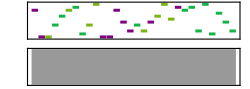

```mathematica
Sound[SoundNote[#,1,RandomChoice[{"Piano","Cello","Tuba"}]]&/@RandomInteger[12,30],4]
```

```mathematica
EmitSound[%389]
```

```mathematica
EmitSound[%379]
```

```mathematica
Plot[,{x,0,20},MeshFunctions->{Function[{x,y},y]},Mesh->{{0}},MeshStyle->Directive[PointSize[Medium],Red]]
```

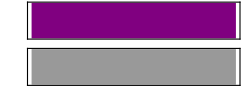

```mathematica
Sound[SoundNote[50]]
```

```mathematica
EmitSound[%376]
```

```mathematica
EmitSound[%374]
```

```mathematica
Sound[SampledSoundList[Table[Sin[2 π 500 t],{t,0,1,1./2000}],2000]]
```

-Graphics-

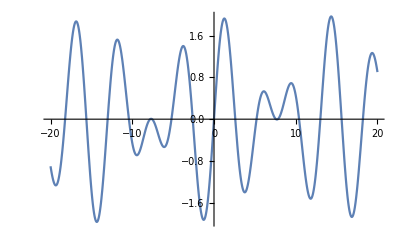

This function plots Sin[Sqrt[2] x]+Sin[x]. This function has  a total of 18 extremas . A proposed description of this plot based on the derivatives and extremas : still a smooth decline that ends at x = -19.3542 then a sharp increase that ends at x = -16.8648 then a sharp decrease that ends at x = -14.3389 then a sharp increase that ends at x = -11.8286 then a smooth decline that ends at x = -9.44122 then a very smooth increase that ends at x = -7.69644 then still a smooth decline that ends at x = -6.09682 then a smooth increase that ends at x = -3.76467 then a sharp decrease that ends at x = -1.26326 then a sharp increase that ends at x = 1.26326 then a sharp decrease that ends at x = 3.76467 then a smooth increase that ends at x = 6.09682 then still a smooth decline that ends at x = 7.69644 then a very smooth increase that ends at x = 9.44122 then a smooth decline that ends at x = 11.8286 then a sharp increase that ends at x = 14.3389 then a sharp decrease that ends at x = 16.8648 then a sharp increase that ends at x = 19.3542 then still a smooth decline that ends at x = 20

```mathematica
f["Sin[Sqrt[2] x]+Sin[x]",-20,20]
```

```mathematica
Sound[SoundNote[0]]
```

-Graphics-

```mathematica
EmitSound[Sound[SoundNote[0]]]
```

```mathematica
Sound[SampledSoundFunction[Sin[0.125 #]&,4000,200]]
```

-Graphics-

```mathematica
[0]
```

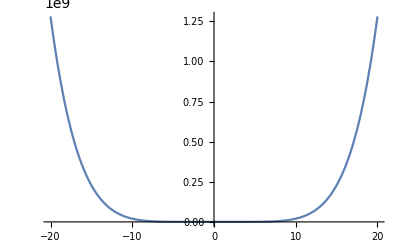

This function plots 20*x^6. This function is polynomial. The exponent of this function is 6. This function has  a total of 10 extremas . A proposed description of this plot based on the derivatives and extremas : still a smooth decline that ends at x = 0. then a very smooth increase that ends at x = 0. then a very smooth increase that ends at x = 0. then a very smooth increase that ends at x = 0. then a very smooth increase that ends at x = 0. then a very smooth increase that ends at x = 20

```mathematica
f["20*x^6",-20,20]
```

```mathematica
PolynomialQ[Sin[x]]
```

True

```mathematica
na = Table[RandomInteger[{1,1000}],100];
```

```mathematica
xa = Table[RandomInteger[{1,1000}],100];
```

```mathematica
da = Table[RandomInteger[{1,1000}],100];
```

```mathematica
exp = Table[RandomInteger[{1,10}],100];
```

```mathematica
NetModel["Inception V3 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
CloudGet["https://www.wolframcloud.com/objects/b14bc770-5d09-40b1-a4fb-19c9de229548"] (*Evaluate this cell to copy the example input from a cloud object*)
```

```mathematica
weights=NetExtract[NetModel["Inception V3 Trained on ImageNet Competition Data"],{"conv_conv2d","Weights"}];
```

```mathematica
Merge[{association,association1},Flatten]
```

```mathematica
association1test = Table[Binarize[Plot[ (da[[xal]]+(x))/(x)+na[[xal]],{x,-10,10},Axes-> False,PlotRange->{-1000,1000}]]-> "Hyperbolic",{xal,1,100,1}];
```

```mathematica
association1 = Table[Binarize[Plot[ (da[[xal]]+(x))/(x)+na[[xal]],{x,-10,10},Axes-> False,PlotRange->{-1000,1000}]]-> "Hyperbolic",{xal,1,1000,1}];
```

```mathematica
Merge[{associationtest,association1test}]
```

```mathematica
associationtest = Table[Binarize[Plot[ ((da[[xal]])*(x^2))+x,{x,-10,10},Axes-> False,PlotRange->{-1000,1000}]]-> "Parabola",{xal,1,100,1}];
```

```mathematica
TrainSet =Join[association,association1];
```

```mathematica
TestSet = Join[associationtest,association1test];
```

```mathematica
association = Table[Binarize[Plot[ ((da[[xal]])*(x^2))+x,{x,-10,10},Axes-> False,PlotRange->{-1000,1000}]]-> "Parabola",{xal,1,1000,1}];
```

```mathematica
tempNet=Take[NetModel["Inception V3 Trained on ImageNet Competition Data"],{1,-4}]
```

NetChain[<>]

```mathematica
newNet=NetChain[<|"pretrainedNet"->tempNet,"linearNew"->LinearLayer[],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",{"Parabola","Hyperbolic"}}]]
```

NetChain[<>]

```mathematica
trainedNet=NetTrain[newNet,TrainSet,LearningRateMultipliers->{"linearNew"->1,_->0},TargetDevice->"GPU"]
```

NetTrain::trgrestart: TargetDevice -> "GPU" requires a restart of your Wolfram Language session.

$Failed

```mathematica
TrainSet
```

```mathematica
newNet=NetChain[<|"pretrainedNet"->tempNet,"linearNew"->LinearLayer[],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",{"Parabola","Hyperbolic"}}]]
```

NetChain::netinvnodes: tempNet is not a layer, a net, or a valid specification for one.

$Failed

```mathematica
trainedNet=NetTrain[newNet,TrainSet,LearningRateMultipliers->{"linearNew"->1,_->0}]
```

NetTrain::invnet: First argument to NetTrain should be a fully specified net.

$Failed

```mathematica
ClassifierMeasurements[trainedNet,TestSet,"Accuracy"]
```

0.69

```mathematica
hey
```